# E-model (n=1)

# This notebook is a part of my Diploma Thesis with title “Swampland Conjectures and Constraints on Inflation” . The knowledge of the theoretical results is important, if someone wishes to follow the presented results in this notebook. My Thesis can be found in an other file in my GitHub repository.

## Definition of the Potential and Introduction of the Slow-Roll parameters

## In this section we will introduce the potential and the slow-roll parameters

```mathematica
v[x_]:=Λ^4*(1-Exp[-√2 x*((√(3*w))/k)^(-1)])^2
ε1=a/(2*k^2)*(v'[x]/v[x])^2// Simplify;
ε2=-a/k^2*(v''[x]/v[x])+ε1// Simplify;
ε=ε1/a// Simplify;
η=1/k^2*(v''[x]/v[x])// Simplify;
η1=a*η// Simplify;
```

It is required by the theory that the period of inflation should stop when the flatness conditions are a not satisfied, so when ε1 = 1.

```mathematica
Solve[ε1==1,x]
```

{{x→ConditionalExpression[(√(3/2) √w (2 ⅈ π C[1]+Log[(-2 √3 √a+3 √w)/(3 √w)]))/k, C[1]∈ℤ]},{x→ConditionalExpression[(√(3/2) √w (2 ⅈ π C[1]+Log[(2 √3 √a+3 √w)/(3 √w)]))/k, C[1]∈ℤ]}}

We have to choose second possible solution, so we set with xf the final value for the φ.

```mathematica
xf=(√(3/2) √w (Log[(2 √3 √a+3 √w)/(3 √w)]))/k// Simplify
```

(√(3/2) √w Log[1+(2 √a)/(√3 √w)])/k

We proceed to the calculation of the initial value of φ , which denoted as xi
Firstly, the integral for the e-folding number is calculated.

```mathematica
Integrate[-(k^2/a)*(v[x]/v'[x]),x]
```

-(√(3/2) k √w ((√(3/2) ⅇ^((√(2/3) k x)/(√w)) √w)/k-x))/(2 a)

```mathematica
Solve[-(√(3/2) k √w ((√(3/2) ⅇ^((√(2/3) k xf)/(√w)) √w)/k))/(2 a)-(-(√(3/2) k √w ((√(3/2) ⅇ^((√(2/3) k x)/(√w)) √w)/k))/(2 a))==Y,x]
```

{{x→ConditionalExpression[(√(3/2) √w (2 ⅈ π C[1]+Log[(2 √3 √a √w+3 w+4 a Y)/(3 w)]))/k, C[1]∈ℤ]}}

```mathematica
xi=(√(3/2) √w (Log[(2 √3 √a √w+3 w+4 a Y)/(3 w)]))/k// Simplify
```

(√(3/2) √w Log[1+(2 √a)/(√3 √w)+(4 a Y)/(3 w)])/k

# Calculation of the observational indices

We calculate the slow-roll parameters for
φ = φi and we take the Taylor approximation for N → ∞. Afterwards, we
calculate the primordial density perturbation and the tensor to scalar ratio for φ = φi and we start our primary work.

```mathematica
ε1i=ε1 /. x->xi// Simplify;
ε2i=ε2 /. x->xi// Simplify;
εi=ε /. x->xi// Simplify;
η1i=η1 /. x->xi// Simplify;
ηi=η/. x->xi// Simplify;
```

Taylor approximation for N → ∞

```mathematica
Series[εi,{Y,Infinity,2}];
Series[ε1i,{Y,Infinity,2}];
Series[ε2i,{Y,Infinity,2}];
Series[ηi,{Y,Infinity,2}];
Series[η1i,{Y,Infinity,2}];
```

```mathematica
εi=(3 w)/(4 a^2 Y^2)//Simplify;
ε1i=(3 w)/(4 a Y^2)//Simplify;
ε2i=1/(a Y)+(-2 √3 √a √w-3 w+3 a w)/(4 a^2 Y^2)//Simplify;
ηi=-1/(a Y)+((√3 √w)/(2 a^(3/2))+(3 w)/(4 a^2))/Y^2//Simplify;
η1i=-1/Y+((√3 √w)/(2 √a)+(3 w)/(4 a))/Y^2//Simplify;
```

We set Y=60

```mathematica
εi60=εi/.Y->60//Simplify;
ε1i60=ε1i/. Y->60//Simplify;
ε2i60=ε2i/. Y->60//Simplify;
ηi60=ηi/. Y->60//Simplify;
η1i60=η1i/. Y->60//Simplify;
```

w/(4800 a^2)

w/(4800 a)

(-2 √3 √a √w-3 w+3 a (80+w))/(14400 a^2)

(-240 a+2 √3 √a √w+3 w)/(14400 a^2)

(-240 a+2 √3 √a √w+3 w)/(14400 a)

We proceed with the primordial density perturbation and the tensor to scalar ratio :

```mathematica
ns=1-6*ε1i+2*η1i// Simplify;
ns60=ns/. Y->60// Simplify
r=16*ε1i// Simplify;
r60=r/.Y->60//Simplify
```

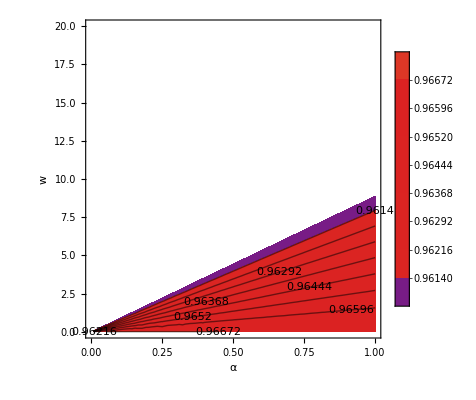

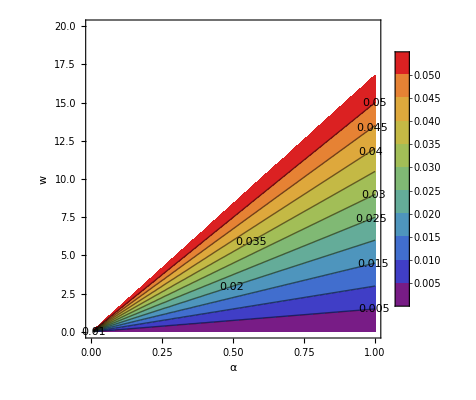

```mathematica
ContourPlot[ns60,{a,0,1},{w,0.01,20},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","w"},Contours->10,PlotRange->{0.9607,0.9691}]
ContourPlot[r60,{a,0,1},{w,0.01,20},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","w"},Contours->10,PlotRange->{0,0.056}]
```

We proceed with the calculation of the contour plots of the slow-roll parameters

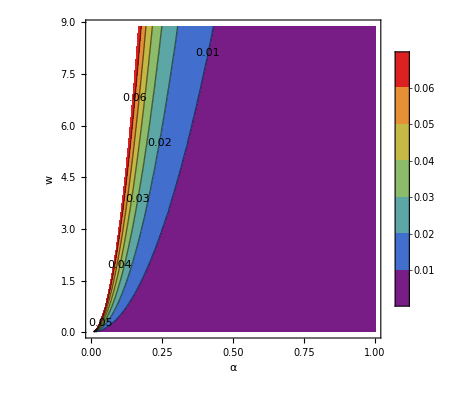

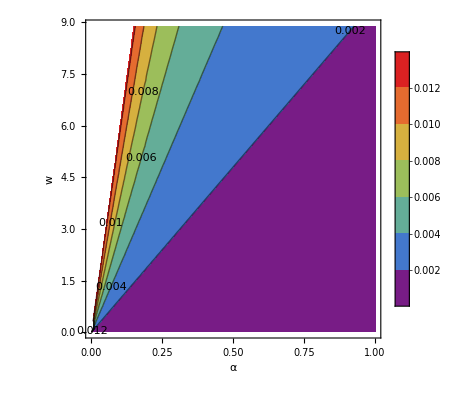

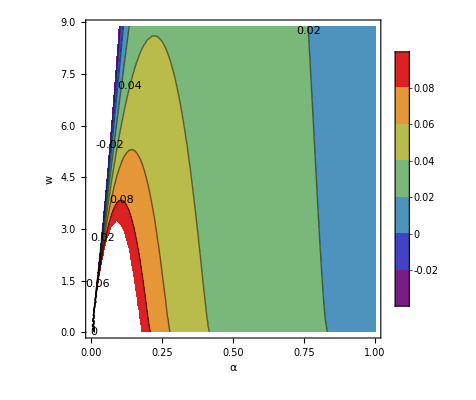

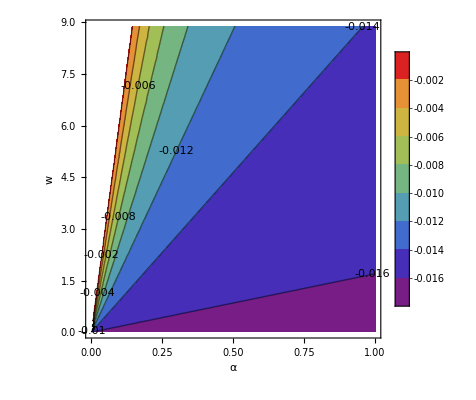

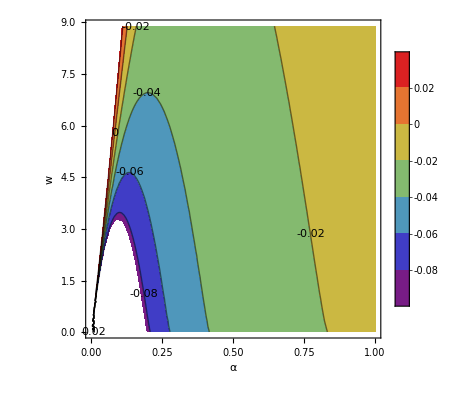

```mathematica
ContourPlot[εi60,{a,0,1},{w,0.01,8.887},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","w"}]
ContourPlot[ε1i60,{a,0,1},{w,0.01,8.887},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","w"}]
ContourPlot[ε2i60,{a,0,1},{w,0.01,8.887},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","w"}]
ContourPlot[η1i60,{a,0,1},{w,0.01,8.887},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","w"}]
ContourPlot[ηi60,{a,0,1},{w,0.01,8.887},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","w"}]
```

## Swampland Conjectures

• The Swampland Distance Conjecture limits the validity of an E.F.T.
and set an upper limit for the traversable by the scalar field as following

                                  ∆φ ≤ f ∼ O(1), in natural units

• The De Sitter Conjecture. It declares that it is impossible to create
De Sitter vacua in string theory. This leads us to set of a lower limit
for the gradient of scalar potentials [Tri20]:
V’/V≥ g ∼ O(1). 
• Another important result is the following -V”/V≥ g ∼ O(1).

```mathematica
s=v'[x]/v[x]// Simplify;
sinitial=s/. x->xi// Simplify;
sinitial60=sinitial/. Y->60// Simplify;
sinitial60k=sinitial60/. k->1// Simplify
```

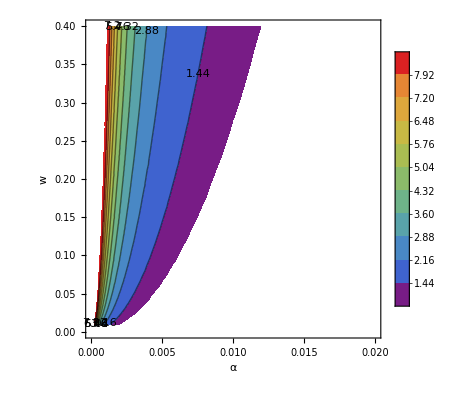

```mathematica
ContourPlot[sinitial60k,{a,0,0.02},{w,0.01,0.4},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","w"},Contours->10,PlotRange->{1,9}]
```

```mathematica
s1=-v''[x]/v[x]// Simplify;
s1initial=s1/. x->xi// Simplify;
s1initial60=s1initial/. Y->60// Simplify;
s1initial60k=s1initial60/. k->1// Simplify
```

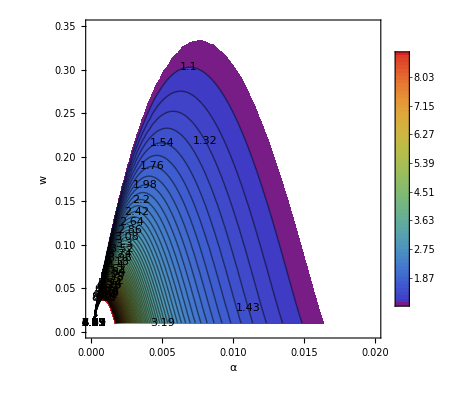

```mathematica
ContourPlot[s1initial60k,{a,0,0.02},{w,0.01,0.35},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","w"},Contours->70,PlotRange->{1,9}]
```

At this point we have some calculations for a=1. This is the General Relativity limit.

```mathematica
ns60gr=ns60/.a->1
```

(3480+√3 √w-3 w)/3600

```mathematica
Reduce[ns60gr>0.9607,w]
Reduce[ns60gr<0.9691,w]
```

```mathematica
r60gr=r60/.a->1
```

w/300

```mathematica
Reduce[r60gr<0.056,w]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

w<16.8

The Swampland Criteria are tested in the next steps.

```mathematica
sinitial60kgr=sinitial60k/. a->1
```

(√6 √w)/(120+√3 √w)

```mathematica
Reduce[(√6 √w)/(120+√3 √w)>1,w]//N
```

w>27976.5

```mathematica
s1initial60kgr=s1initial60k/.a->1
```

(240+2 √3 √w-3 w)/(120+√3 √w)^2

```mathematica
Reduce[(240+2 √3 √w-3 w)/(120+√3 √w)^2>1,w]//N
```

False